# Question 1

a)

```mathematica
A = Table[Prime[n],{n,100}]
```

```mathematica
{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}
```

25 of the numbers between 1 and 100 are prime.

b)

```mathematica
counter = 0;
For[i = 1, i <= 100,i++, If[PrimeQ[2^i-1] == True,counter ++,]]
Print[counter]
```

10

There are 10 numbers between 1 and 100 that are prime and of the form 2^n-1.

# Question 2

a)

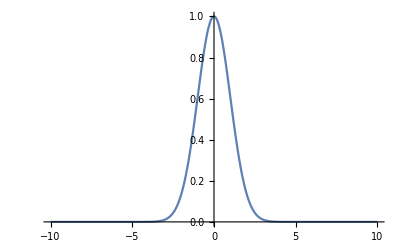

```mathematica
F[x_] := c *Exp[-((x-xb)^2)/(2(Dx^2))];
c = 1;
xb = 0;
Dx = 1;

Plot[F[x], {x,-10,10},PlotRange->{0,1}]
```

```mathematica
Clear[xb,Dx]
```

b)

{1→1,xb→1,Dx→1}

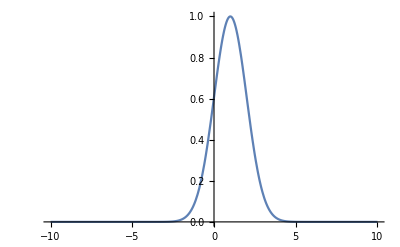

```mathematica
sub = {c -> 1,xb -> 1 ,Dx ->1}
Plot[F[x]/.sub, {x,-10,10},PlotRange->{0,1}]
```

{1→1,xb→2,Dx→2}

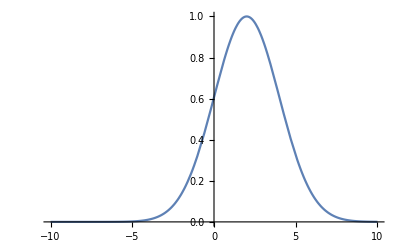

```mathematica
Clear[xb,Dx]
sub = {c -> 1,xb -> 2 ,Dx ->2}
Plot[F[x]/.sub, {x,-10,10},PlotRange->{0,1}]
```

{1→1,xb→1,Dx→2}

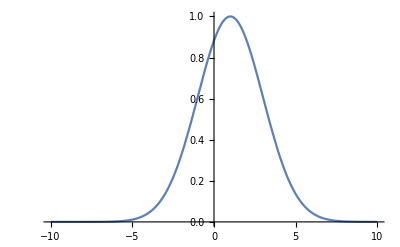

```mathematica
Clear[xb,Dx]
sub = {c -> 1,xb -> 1,Dx ->2}
Plot[F[x]/.sub, {x,-10,10},PlotRange->{0,1}]
```

{1→1,xb→8,Dx→3}

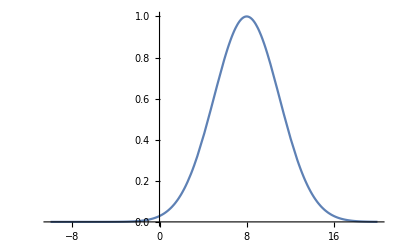

```mathematica
Clear[xb,Dx]
sub = {c -> 1,xb -> 8,Dx ->3}
Plot[F[x]/.sub, {x,-10,20},PlotRange->{0,1}]
```

{1→1,xb→1,Dx→5}

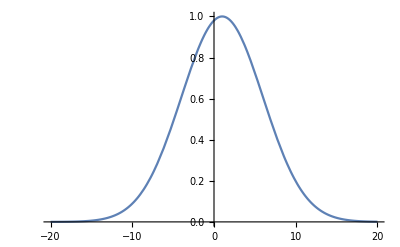

```mathematica
Clear[xb,Dx]
sub = {c -> 1,xb -> 1,Dx ->5}
Plot[F[x]/.sub, {x,-20,20},PlotRange->{0,1}]
```

xb results in plot shifting either to the right or left when it is increased and Dx makes gaussian curve more widen.
xb is µ; the average and Dx is sigma; the standard deviation. Therefore an increase in the average results in 
a shift such that the curve is centered at the average and an increase in standard deviation affects the width
of the plot since it changes the variance.

C.

```mathematica
1/Integrate[F[x], {x,-Infinity,Infinity}]
```

ConditionalExpression[(√(1/Dx^2))/(√(2 π)),Re[Dx^2]≥0]

Solving for C we get 1/√2π(Dx)^2

D.

```mathematica
F[x_] := c*Exp[-((x-xb)^2)/(2(Dx^2))];
c = 1/Sqrt[2π(Dx)^2];
Integrate[F[x], {x,xb-2.5*Dx,xb + 2.5*Dx}]
```

(0.987581 Dx)/(√(Dx^2))

Dx/Dx^2  simplifies to 1 so the fraction of the distribution is 0.987581

# Question 3

a)

{}

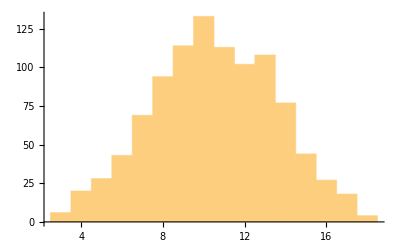

```mathematica
ls = {}
For[i =1,i ≤1000,i++,
DiceRoll1= Ceiling[Random[]*6];
DiceRoll2= Ceiling[Random[]*6];
DiceRoll3= Ceiling[Random[]*6];
sum =  DiceRoll1 + DiceRoll2 + DiceRoll3 ;
ls =Append[ls,sum];
];
Histogram[ls]
```

The histogram represents the number of time each sum occurs in a simulated game of 1000 dice rolls.

b)

{}

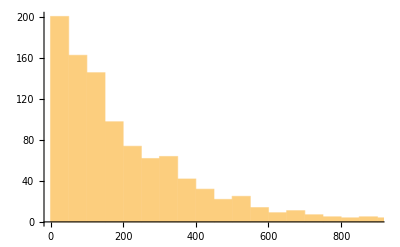

```mathematica
ls = {}
For[i =1,i ≤1000,i++,
counter = 0;
DiceRoll1= Ceiling[Random[]*6];
DiceRoll2= Ceiling[Random[]*6];
DiceRoll3= Ceiling[Random[]*6];
While[ Ceiling[Random[]*6]+ Ceiling[Random[]*6]+ Ceiling[Random[]*6]!= 18,counter +=1];
ls =Append[ls,counter];
];
Histogram[ls]
```

The amount of time one would expect to roll a triple 6 is geometrically distributed.

c)

```mathematica
average = Total[ls]/Length[ls]//N
```

213.669

Since this is geometrically distributed then theoretically the average is 1/p, where p is the probability 
which is 1/216.
There for the theoretical average is 216 which close to 213.669.